Результаты (метод Эйлера)

0 |      0
 0.00000 |  0.10000
-0.02000 |  0.14000
-0.04800 |  0.15600
-0.07920 |  0.16240
-0.11168 |  0.16496
-0.14467 |  0.16598
-0.17787 |  0.16639
-0.21115 |  0.16656
-0.24446 |  0.16662
-0.27778 |  0.16665

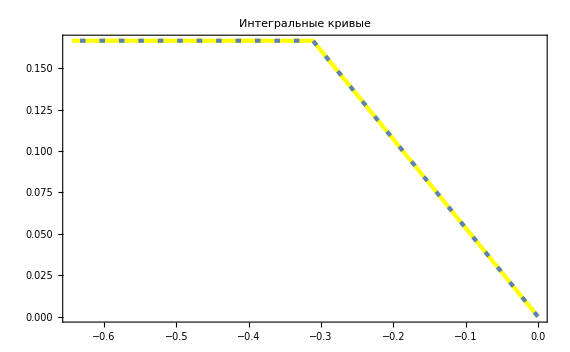

```mathematica
f[x_,y_]:=-2*y;
g[x_,y_]:= -6*y+1;
{a,b}={0,1}; {x0,y0}={0,0};
h=0.1;
Clear[x];
{x,y}={x0,y0};
xlst = List[{y0,x0}];
ylst = List[{x0,y0}];
m = Floor[(b - a)/h] + 1;
eul = Table[{x,y}= {x+h*f[x,y], y+h*g[x,y]}, {i, m-1}];
eul = Prepend[eul,{x0,y0}];
Print["Результаты (метод Эйлера)"]
gr1 :=ListPlot[eul]
PaddedForm[TableForm[eul,TableHeadings->lst],{5,5}]
(*Show[{gr1}, PlotLabel->"Кривая решений",Ticks->{Automatic}]*)
For[k = 1, k ≤ m, k++,
	{x, y} = {x+h*f[x,y], y+h*g[x,y]};
	xlst = Append[xlst,{x,y}];
	ylst = Append[ylst,{x,y}]];
lst1 = {AbsoluteThickness[3], RGBColor[1,1,0]};
lst2 = {AbsoluteThickness[3], AbsoluteDashing[{4, 10}]};
gr1 = ListPlot[xlst, Joined -> True,
	PlotStyle -> lst1, DisplayFunction->Identity];
gr2 = ListPlot[ylst, Joined -> True,
	PlotStyle -> lst2, DisplayFunction->Identity];
lst3={Automatic, AbsoluteDashing[{10,4}]};
Show[{gr1,gr2}, AxesOrigin->{1,0},
	AxesStyle->{AbsoluteThickness[2]},Frame->True,
	ImageSize->{570,440},
	PlotLabel->"Интегральные кривые",
	Ticks->{Automatic},
	DisplayFunction->$DisplayFunction]
```